```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
h=1;
(*this is the length of the one-dimensional mesh[1]*)
L1=1.2444414542953002;
```

```mathematica
(*test case 1*)
```

```mathematica
u01[x_,y_]:=1+x + 2 y
Lu01[x_,y_]:=0
gradu01[x_,y_]:={1,2}
u00[x_,y_]:=u01[x,y]^2

u1[x_]:=Sin[2 π x^2/L1^2]
Lu1[x_]:=(4 π (L1^2 Cos[(2 π x^2)/L1^2]-4 π x^2 Sin[(2 π x^2)/L1^2]))/L1^4
gradu1[x_]:=(4 π x Cos[(2 π x^2)/L1^2])/L1^2
```

```mathematica
(*check for u00,u01*)
```

```mathematica
t00=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/u_0_0.csv"];
t00=Table[{t00[[i,2]],t00[[i,3]],t00[[i,1]]},{i,2,Length[t00]}]
```

```mathematica
t01=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/u_0_1.csv"];
t01=Table[{t01[[i,2]],t01[[i,3]],t01[[i,1]]},{i,2,Length[t01]}]
```

```mathematica
δ00=Max[Table[Abs[t00[[i,3]]-u00[t00[[i,1]],t00[[i,2]]]],{i,1,Length[t00]}]]
δ01=Max[Table[Abs[t01[[i,3]]-u01[t01[[i,1]],t01[[i,2]]]],{i,1,Length[t01]}]]
Max[δ00,δ01]
```

-∞

4.79616×10^-14

4.79616×10^-14

```mathematica
plotexact00=Plot3D[u00[x,y],{x,0,L},{y,0,h},PlotRange->Full,PlotStyle->{Red,Opacity[0.1]}]
plotexact01=Plot3D[u01[x,y],{x,0,L},{y,0,h},PlotRange->Full,PlotStyle->{Green,Opacity[0.1]}]
```

-Graphics3D-

-Graphics3D-

```mathematica
plotnum00=ListPointPlot3D[t00,PlotRange->Full,PlotStyle->Red,AspectRatio->Automatic]
```

-Graphics3D-

```mathematica
plotnum01=ListPointPlot3D[t01,PlotRange->Full,PlotStyle->{Red,PointSize->0.005}]
```

-Graphics3D-

```mathematica
Show[plotexact00,plotnum00]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics3D-,plotnum00]

```mathematica
Show[plotexact01,plotnum01]
```

-Graphics3D-

```mathematica
Show[plotexact00,plotnum00,plotexact01,plotnum01,PlotRange->Full]
```

-Graphics3D-

```mathematica
(*check for u1*)
```

```mathematica
t1=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/u_1.csv"][[2;;]];
t1=Table[{t1[[i,2]],t1[[i,1]]},{i,2,Length[t1]}]
```

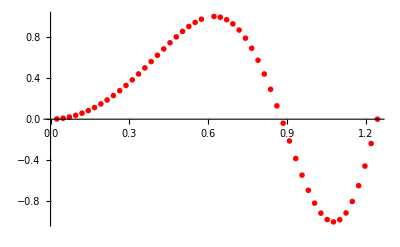

```mathematica
plotnum1=ListPlot[t1,PlotStyle->{Red,PointSize->0.01}]
```

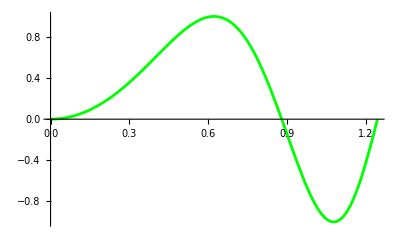

```mathematica
plotexact1=Plot[u1[x],{x,0,L1},PlotRange->Full,PlotStyle->Green]
```

```mathematica
δ=Max[Table[Abs[t1[[i,2]]-u1[t1[[i,1]]]],{i,1,Length[t1]}]]
```

9.7324×10^-6

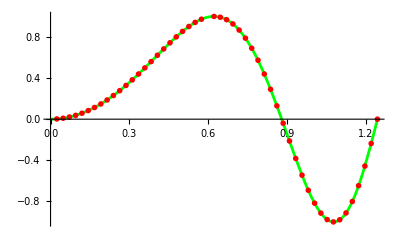

```mathematica
Show[plotexact1,plotnum1]
```